### Inicialização

```mathematica
ud=0.1;
uc=0.01;
um=0.001;
uu=10^-6;
un=10^-9;
uA=10^-10;
up=10^-12;
uD=10;
uh=100;
uk=1000;
uM=10^6;
uG=10^9;
```

```mathematica
me=9.10938356*10^-31;
NA=6.022*10^23;
qe=1.602*10^-19;
Vmol=22.4*10^-3;
R=8.3144598;
T0=273.15;
h=6.626070040×10^−34;
hb=h/(2 Pi);
c=299792458;
kB=1.38064852×10^−23;
eV=qe;
g=9.81;
```

### Problem Set 1

#### 1.1

```mathematica
6*2^3*3^2
```

432

```mathematica
Log@(6*8*9)
```

Log[432]

```mathematica
N[Log[432]]
```

6.06843

```mathematica
(1/6 Log@6+1/3 Log@3+1/2 Log@2)kB*300
```

4.18918×10^-21

```mathematica
N[Log[2]/2+Log[3]/3+Log[6]/6]
```

1.0114

```mathematica
N[Log[432]]
```

6.06843

```mathematica
%^(1/6)
```

2^(2/3) √3

```mathematica
432^(1/3)
```

6 2^(1/3)

```mathematica
kB
```

1.38065×10^-23

```mathematica
T kB/6
```

2.30108×10^-24 T

```mathematica
N@300 *kB(1/6 Log@6+1/3 Log@3+1/2 Log@2)
```

4.18918×10^-21

```mathematica
N@%
```

6.90324×10^-22 Ln[432.]

#### 1.2

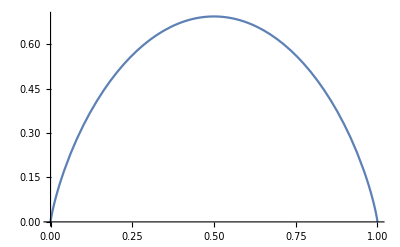

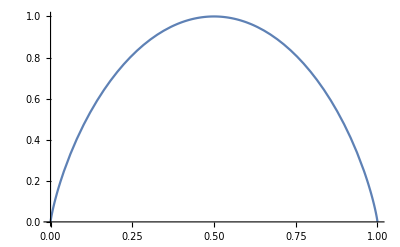

```mathematica
H[p_]=p Log@((1-p)/p)-Log@(1-p);
H2[p_]=-(p Log@p +(1-p)Log@(1-p))/Log@2;
Plot[H[p],{p,0,1}]
Plot[H2[p],{p,0,1}]
```

```mathematica
Log@2
```

Log[2]

```mathematica
1/N[Log[2]]
```

1.4427

```mathematica
N[Log[2]/2+Log[3]/3+Log[6]/6]
```

1.0114

```mathematica
N[(Log@432)/6]
```

1.0114